#### Function

```mathematica
p[dim_] := Flatten[Table[{Symbol["p"<>ToString@i]},{i,1,dim}]];
μ[dim_] := Flatten[Table[{Symbol["μ"<>ToString@i]},{i,1,dim}]];
σ[dim_] := Flatten[Table[{Symbol["σ"<>ToString@i]},{i,1,dim}]];
GaussianMixtureDist[list_,dim_]:=Module[{𝒟,gmm,pxi,grouped},{p[dim],μ[dim],σ[dim]};
𝒟=MixtureDistribution[p[dim],Table[NormalDistribution[μ[dim][[s]],σ[dim][[s]]],{s,dim}]];
gmm=Quiet@EstimatedDistribution[list,𝒟];
gmm
]
GaussianMixtureClustering[list_,dim_]:=Module[{𝒟,mixC,gmm,pxi,grouped},
gmm=GaussianMixtureDist[list,dim];
mixC=Transpose@{First[gmm],Last[gmm]};
pxi=Transpose@Table[dist[[1]] PDF[dist[[2]],list],{dist,mixC}];
grouped = Partition[Flatten[Table[{Ordering[pxi[[s]],-1],list[[s]]},{s,Length[pxi]}]],2];
Table[s[[;;,2]],{s,GatherBy[grouped,First]}]]
```

#### Test

```mathematica
testdist = MixtureDistribution[{1,1,1,1},{NormalDistribution[0,0.5],NormalDistribution[2,0.5],NormalDistribution[4,0.5],NormalDistribution[6,0.5]}]
```

MixtureDistribution[{1,1,1,1},{NormalDistribution[0,0.5],NormalDistribution[2,0.5],NormalDistribution[4,0.5],NormalDistribution[6,0.5]}]

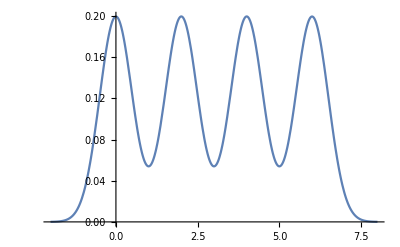

```mathematica
Plot[PDF[testdist,x],{x,-2,8}]
```

```mathematica
testdata = RandomVariate[testdist,1000];
```

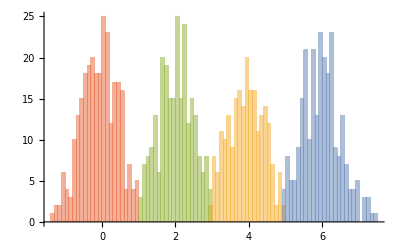

```mathematica
Histogram[GaussianMixtureClustering[testdata,4],{0.1}]
```